# General Poincare map

## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/pcs/Desktop/Breaking time reversal symmetry/Klein group

```mathematica
LaunchKernels[10]
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

```mathematica
Clear[F,Fun,Funinv];
F[α_,k_,s_]:=Module[{a,sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}
];
Fun[α_,k_,s_]:=Module[{sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}.s
];
Funinv[α_,k_,s_]:=Module[{sx=s[[1]]},
MatrixPower[{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}},-1].s
];

Clear[change2];
change2[Q_]:=Module[{B=Norm[Q]},
{Q[[1]]*Sqrt[1-(1/4)B^2],Q[[2]]*Sqrt[1-(1/4)B^2],(1/2)B^2 -1}
];

Clear[mapeo];
mapeo[Qini_,α_,k_,n_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Fun[α,k,#]&,s,n];
Map[change[#]&,list]
];

Clear[mapeoinv];
mapeoinv[Qini_,α_,k_,n_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Funinv[α,k,#]&,s,n];
Map[change[#]&,list]
];

mapeob[Qini_,α_,k_,n_]:=Module[{map={},snew,a,s,Qnew},
AppendTo[map,Qini];
s=change2[Qini];
Do[
snew=MatrixPower[N[F[α,k,s]],2].s;
AppendTo[map,change[snew]];
s=snew;
,{l,1,n}];
map
];

Clear[Jx,Jy,Jz,M,mapeo1,jmas];
Jx[x_,y_,z_,α_,k_]:=x*Cos[α]-y*Sin[α]*Cos[k*x]+z*Sin[α]*Sin[k*x];
Jy[x_,y_,z_,α_,k_]:=x*Sin[α]+y*Cos[α]*Cos[k*x]-z*Cos[α]*Sin[k*x];
Jz[x_,y_,z_,α_,k_]:=y*Sin[k*x]+z*Cos[k*x];

M[Jini_,α_Real,k_Real]:=Module[{M},
M={{D[Jx[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},
{D[Jy[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},{D[Jz[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}}}//N;
M
];

mapeo1[si_,α_,k_,n_]:=Module[{s=si},
MatrixPower[F[α,k,s],n].s
];
```

```mathematica
F[α_,k_,s_]:=Module[{a,sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}
];
```

## Poincare maps

```mathematica
Clear[rot];
rot[θ_]:={{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}};
Clear[Tx,Ty,Tz];
Tx=DiagonalMatrix[{1,-1,-1}];
Ty=DiagonalMatrix[{-1,1,-1}];
Tz=DiagonalMatrix[{-1,-1,1}];
Clear[T1,T2,T3];
T1[α_]:={{-Cos[α],-Sin[α],0},{-Sin[α],Cos[α],0},{0,0,1}};
T2[α_]:={{Cos[α],Sin[α],0},{Sin[α],-Cos[α],0},{0,0,1}};
T3=Tz;
Clear[Rz];
Rz[α_]:={{Cos[α],-Sin[α],0},{Sin[α],Cos[α],0},{0,0,1}};
Clear[com];
com[a_,b_]:=a.b-b.a;
Clear[change];
change[s_]:=Module[{B=Sqrt[2/(1-s[[3]])]},
{s[[1]]*B,s[[2]]*B}
];
```

```mathematica
Clear[Rxx,Raxis];
Raxis[theta_,n_]:=Module[{u=Normalize[n],nx,ny,nz,c=Cos[theta],s=Sin[theta]},
{nx,ny,nz}=u;
{{c+nx^2 (1-c),nx ny (1-c)-nz s,nx nz (1-c)+ny s},{ny nx (1-c)+nz s,c+ny^2 (1-c),ny nz (1-c)-nx s},{nz nx (1-c)-ny s,nz ny (1-c)+nx s,c+nz^2 (1-c)}}
];
Rxx[k_,s_]:={{1,0,0},{0,Cos[k*s[[1]]],-Sin[k*s[[1]]]},{0,Sin[k*s[[1]]],Cos[k*s[[1]]]}};
Clear[map];
map[theta_,n_,k_,s_,kicks_]:=NestList[Raxis[theta,n].Rxx[k,#].#&,s,kicks];
```

```mathematica
Clear[mapeo];
mapeo[Qini_,α_,k_,n_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Fun[α,k,#]&,s,n];
Map[change[#]&,list]
];
Clear[T1,T2];
T1[α_]:={{-Cos[α],-Sin[α]},{-Sin[α],Cos[α]}};
T2[α_]:={{Cos[α],Sin[α]},{Sin[α],-Cos[α]}};
```

```mathematica
α=0.84;
k=10.;
```

```mathematica
kicks=1500;
```

```mathematica
ini=RandomPoint[Sphere[],100];
```

```mathematica
n={0,1/3,1};
```

```mathematica
poincare=ParallelTable[map[α,n,k,i,kicks],{i,ini},DistributedContexts->Full];
qppoints=Map[change[#]&,Flatten[poincare,1]];
```

```mathematica
poincare1=Map[T1[α].#&,qppoints];
poincare2=Map[T2[α].#&,qppoints];
```

```mathematica
classic=ListPlot[qppoints,PlotRange->All,PlotStyle->Directive[Black,Opacity[1],PointSize[0.0015]],AspectRatio->1,ImageSize->800,PlotTheme->"Detailed"]
```

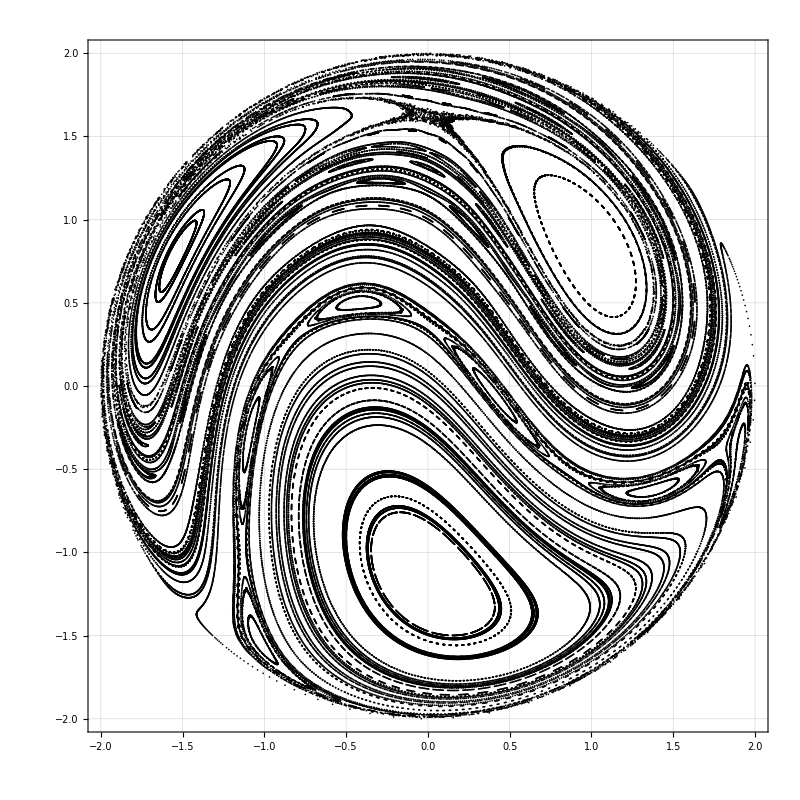

```mathematica
classic=ListPlot[qppoints,PlotRange->All,PlotStyle->Directive[Black,Opacity[1],PointSize[0.0015]],AspectRatio->1,ImageSize->800,PlotTheme->"Detailed"]
```

```mathematica
ListPlot[{poincare1,poincare2,qppoints},PlotRange->All,PlotStyle->{Directive[Blue,Opacity[0.15]],Directive[Red,Opacity[0.15]],Directive[Black,Opacity[1]]},AspectRatio->1,ImageSize->800,PlotTheme->"Detailed"]
```

## Poincare maps, breaking time reversal

```mathematica
Clear[rot];
rot[θ_]:={{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}};
Clear[Tx,Ty,Tz];
Tx=DiagonalMatrix[{1,-1,-1}];
Ty=DiagonalMatrix[{-1,1,-1}];
Tz=DiagonalMatrix[{-1,-1,1}];
Clear[T1,T2,T3];
T1[α_]:={{-Cos[α],-Sin[α],0},{-Sin[α],Cos[α],0},{0,0,1}};
T2[α_]:={{Cos[α],Sin[α],0},{Sin[α],-Cos[α],0},{0,0,1}};
T3=Tz;
Clear[Rz,Rx];
Rx[k_]:={{1,0,0},{0,Cos[k],-Sin[k]},{0,Sin[k],Cos[k]}};
Rz[α_]:={{Cos[α],-Sin[α],0},{Sin[α],Cos[α],0},{0,0,1}};
Clear[com];
com[a_,b_]:=a.b-b.a;
Clear[change];
change[s_]:=Module[{B=Sqrt[2/(1-s[[3]])]},
{s[[1]]*B,s[[2]]*B}
];
```

```mathematica
(*Ry[alpha_,tau_]:={{Cos[alpha*tau],0,Sin[alpha*tau]},{0,1,0},{-Sin[alpha*tau],0,Cos[alpha*tau]}}*)
```

```mathematica
Clear[Rxx,Raxis];
Raxis[theta_,n_]:=Module[{u=Normalize[n],nx,ny,nz,c=Cos[theta],s=Sin[theta]},
{nx,ny,nz}=u;
{{c+nx^2 (1-c),nx ny (1-c)-nz s,nx nz (1-c)+ny s},{ny nx (1-c)+nz s,c+ny^2 (1-c),ny nz (1-c)-nx s},{nz nx (1-c)-ny s,nz ny (1-c)+nx s,c+nz^2 (1-c)}}
];
Rxx[k_,s_]:={{1,0,0},{0,Cos[k*s[[1]]],-Sin[k*s[[1]]]},{0,Sin[k*s[[1]]],Cos[k*s[[1]]]}};
Clear[map];
map[n_,α_,k_,γ_,s_,kicks_]:=NestList[Raxis[γ,{0,1,0}].Raxis[α,n].Rxx[k,#].#&,s,kicks];
```

```mathematica
α=0.84;
k=4.;
n={1,1,1};
γ=1.;
```

```mathematica
kicks=2000;
```

```mathematica
ini=RandomPoint[Sphere[],100];
```

```mathematica
poincare=ParallelTable[map[n,α,k,γ,i,kicks],{i,ini},DistributedContexts->Full];
qppoints=Map[change[#]&,Flatten[poincare,1]];
```

```mathematica
classic=ListPlot[qppoints,PlotRange->All,PlotStyle->Directive[Black,Opacity[1],PointSize[0.0015]],AspectRatio->1,ImageSize->800,PlotTheme->"Detailed"]
```

-Graphics-

# QKT Quantum

## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\Chaotic_eigenfunctions\Breaking time reversal symmetry

```mathematica
(*Clear all cached/memoized definitions*)
ClearAll[sz,sm,sp,sx,sy,sx2,kickPart,twistPart,Floq];
(*Define Sz operator:diagonal with eigenvalues m=-J to J*)
sz[j_]:=sz[j]=DiagonalMatrix[Table[-j+k-1,{k,1,2 j+1}]];
(*Raising operator S_+(superdiagonal)*)
sp[j_]:=sp[j]=DiagonalMatrix[Table[Sqrt[j (j+1)-m (m+1)],{m,-j,j-1}],1];
(*Lowering operator S_-(subdiagonal)*)
sm[j_]:=sm[j]=DiagonalMatrix[Table[Sqrt[j (j+1)-m (m-1)],{m,-j+1,j}],-1];
(*Sx and Sy from ladder operators,defined as sparse for efficiency*)
sx[j_]:=sx[j]=SparseArray[(1/2) (sp[j]+sm[j])];
sy[j_]:=sy[j]=SparseArray[(1/(2 I)) (sp[j]-sm[j])];
(*Precompute Sx^2 for each J only once*)
sx2[j_]:=sx2[j]=sx[j].sx[j];
(*Matrix exponential of the nonlinear "kick" part:exp(-i k/(2J) Sx^2)*)
kickPart[j_,k_]:=kickPart[j,k]=MatrixExp[(-I*k/(2 j)) sx2[j]];
(*Matrix exponential of the linear "twist" part:exp(-i α τ Sz)*)
twistPart[j_,α_,τ_]:=MatrixExp[(-I*α*τ) sz[j]];
(*Final Floquet operator:U=kick.twist*)
Floq[j_,α_,k_,τ_]:=kickPart[j,k].twistPart[j,α,τ];ClearAll[coherentStateGeneratorStable];
coherentStateGeneratorStable=Compile[{{J,_Integer},{q,_Real},{p,_Real}},
Module[{dim,α,result,mVals,logs,maxLog,terms,norm},
dim=2 J+1;
result=ConstantArray[0.0+0. I,dim];
(*Pre-allocate fixed size complex vector*)
α=(q+I p)/Sqrt[4-(q^2+p^2)];
If[Abs[α]==0,result[[1]]=1.0+0. I,
(*Set only the first component*)
mVals=Range[-J,J];
logs=0.5 (LogGamma[2 J+1]-LogGamma[J+1+mVals]-LogGamma[J+1-mVals])+(J+mVals) Log[α];
maxLog=Max[Re[logs]];
terms=Exp[logs-maxLog];
norm=Sqrt[Total[Abs[terms]^2]];
result=terms/norm;];
result],CompilationTarget->"WVM",RuntimeOptions->"Speed",Parallelization->True,RuntimeAttributes->{Listable}];
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

## Grid

```mathematica
radius=1.99999;
delta=0.020;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPointsRaw=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
(*Keep only those inside disk*)
region=Select[gridPointsRaw,Norm[#]<radius&];
```

```mathematica
region//Dimensions
```

{31401,2}

## Phase space

```mathematica
(*Floquet parameters*)
J=300;
d=2 J+1;
α=0.84;
τ=1.0;
k=20.0;
```

```mathematica
Print["Generating coherent states over ",Length[region]," points..."];
statesCompiled=ParallelMap[coherentStateGeneratorStable[J,#[[1]],#[[2]]]&,region,Method->"CoarsestGrained"  (*Optional:better batching*)];
```

Generating coherent states over 31401 points...

```mathematica
Print["Computing Floquet matrix..."];
Clear[mat];
mat=Floq[J,α,k,τ];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
```

Computing Floquet matrix...

```mathematica
Print["Projecting states into Floquet basis..."];
overlaps=Conjugate[neweigenvec].Transpose[statesCompiled];
Print["Computing IPRs..."];
iprCompiled=Total[Abs[overlaps]^4,{1}];
```

Projecting states into Floquet basis...

Computing IPRs...

```mathematica
newdata=Table[-Log[i]/Log[2 J+1],{i,iprCompiled}];
```

```mathematica
(*Generate plot*)
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", τ = "<>ToString[N[τ]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True]
```

-Graphics-

## examples

```mathematica
Show[{d2plotM,classic}]
(*Export["d2_k_5_with_lines.png",Show[{d2plotM,lines}],ImageResolution->300]*)
```

-Graphics-

# Generalized QKT

## Tests

```mathematica
(*ClearAll[generateSpinOperators];
generateSpinOperators[J_]:=Module[{d=2 J+1,m,x,y,z},m=Range[-J,J];
z=DiagonalMatrix[m];
x=1/2 SparseArray[Band[{1,2}]->Table[Sqrt[J (J+1)-m[[i]] (m[[i+1]])],{i,d-1}],{d,d}]+Transpose@SparseArray[Band[{1,2}]->Table[Sqrt[J (J+1)-m[[i]] (m[[i+1]])],{i,d-1}],{d,d}];
y=1/(2 I) SparseArray[Band[{1,2}]->Table[Sqrt[J (J+1)-m[[i]] (m[[i+1]])],{i,d-1}],{d,d}]-Transpose@SparseArray[Band[{1,2}]->Table[Sqrt[J (J+1)-m[[i]] (m[[i+1]])],{i,d-1}],{d,d}];
<|"Jx"->x,"Jy"->y,"Jz"->z|>];

ops=generateSpinOperators[J];
{x,y,z}=Lookup[ops,{"Jx","Jy","Jz"}];

u.{Jx,Jy,Jz}

R=N[MatrixExp[-I α (u.{x,y,z})]];

ClearAll[FloqnFast];
FloqnFast[J_,α_,k_,n_]:=Module[{ops,u,R,U2},ops=generateSpinOperators[J];
u=Normalize[n];
R=u.Lookup[ops,{"Jx","Jy","Jz"}];
U2=N[MatrixExp[-I α R]];
kickPart[J,k].U2];

ClearAll[rotationGenerator];
rotationGenerator[J_,n_]:=Module[{ops,u},ops=generateSpinOperators[J];
u=Normalize[n];
u.Lookup[ops,{"Jx","Jy","Jz"}]];

R=rotationGenerator[J,n];
U2[α_]:=N[MatrixExp[-I α R]];*)
```

## Setup

```mathematica
SetDirectory[NotebookDirectory[]];
Get["QKT.wl"];
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

## Grid

```mathematica
radius=1.99999;
delta=0.020;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPointsRaw=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
(*Keep only those inside disk*)
region=Select[gridPointsRaw,Norm[#]<radius&];
region//Dimensions
```

{31401,2}

## Method

```mathematica
Names["QKT`*"]
```

{Floq,Floqn,generateCoherentStateCompiler,generateSpinOperators}

```mathematica
(*Floquet parameters*)
J=500;
d=2 J+1;
α=0.84;
τ=1.0;
k=20.0;
```

```mathematica
ops=generateSpinOperators[J];
```

```mathematica
Print["Generating coherent states over ",Length[region]," points..."];
coherentStateGenerator=generateCoherentStateCompiler[];
statesCompiled=ParallelMap[coherentStateGenerator[J,#[[1]],#[[2]]]&,region,Method->"CoarsestGrained"  (*Optional:better batching*)];
```

Generating coherent states over 31401 points...

```mathematica
Print["Computing Floquet matrix..."];
Clear[mat];
mat=U;
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
```

Computing Floquet matrix...

```mathematica
Print["Projecting states into Floquet basis..."];
overlaps=Conjugate[neweigenvec].Transpose[statesCompiled];
Print["Computing IPRs..."];
iprCompiled=Total[Abs[overlaps]^4,{1}];
```

Projecting states into Floquet basis...

Computing IPRs...

```mathematica
newdata=Table[-Log[i]/Log[2 J+1],{i,iprCompiled}];
```

```mathematica
(*Generate plot*)
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", τ = "<>ToString[N[τ]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True]
```

-Graphics-

```mathematica
?Floqn
```

```mathematica
nList=Normalize/@Table[{Cos[θ],0,Sin[θ]},{θ,0,Pi/2,Pi/40}];
```

```mathematica
(*matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];*)
```

```mathematica
Do[
Print["Computing Floquet matrix..."];
mat=Floqn[J,α,k,N[n]];
neweigenvec=Orthogonalize[Eigenvectors[mat]];
Print["Projecting states into Floquet basis..."];
overlaps=Conjugate[neweigenvec].Transpose[statesCompiled];
Print["Computing IPRs..."];
iprCompiled=Total[Abs[overlaps]^4,{1}];
(*Generate plot*)
Print["Printing plot..."];
newdata=Table[-Log[i]/Log[2 J+1],{i,iprCompiled}];
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", n = "<>ToString[N[n]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True];
Export["d2_k_"<>ToString[NumberForm[k,{4,2}]]<>".png",plot];

,{n,nList}]
```

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Printing plot...

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Printing plot...

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Printing plot...

Computing Floquet matrix...

Projecting states into Floquet basis...

$Aborted

```mathematica
nList=Table[{0,-Sin[θ],Cos[θ]},{θ,0,Pi,Pi/50}];
nList//Length
```

51

```mathematica
nList=Table[{Sin[θ],0,Cos[θ]},{θ,0,Pi,Pi/100}];
```

```mathematica
alphaStr=StringReplace[ToString[NumberForm[α,{4,2}]],"."->"p"];
kStr=StringReplace[ToString[NumberForm[k,{4,2}]],"."->"p"];
```

```mathematica
Do[
Print["Computing Floquet matrix..."];
mat=Floqn[J,α,k,N[n]];
neweigenvec=Orthogonalize[Eigenvectors[mat]];
Print["Projecting states into Floquet basis..."];
overlaps=Conjugate[neweigenvec].Transpose[statesCompiled];
Print["Computing IPRs..."];
iprCompiled=Total[Abs[overlaps]^4,{1}];
Print["Generating plot..."];
newdata=Table[-Log[i]/Log[2 J+1],{i,iprCompiled}];
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", n = "<>ToString[N[n]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->1000,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True];
(* ===Build safe filename===*)
nxStr=StringReplace[ToString[NumberForm[n[[1]],{4,2}]],"."->"p"];
nyStr=StringReplace[ToString[NumberForm[n[[2]],{4,2}]],"."->"p"];
nzStr=StringReplace[ToString[NumberForm[n[[3]],{4,2}]],"."->"p"];
filename="d2_a_"<>alphaStr<>"_k_"<>kStr<>"_nx_"<>nxStr<>"_ny_"<>nyStr<>"_nz_"<>nzStr<>".png";
Print["Exporting to: ",filename];
Export[filename,plot];,{n,N[nList]}]
```

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p00_ny_0p00_nz_1p00.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p03_ny_0p00_nz_1p00.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p06_ny_0p00_nz_1p00.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p09_ny_0p00_nz_1p00.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p13_ny_0p00_nz_0p99.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p16_ny_0p00_nz_0p99.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p19_ny_0p00_nz_0p98.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p22_ny_0p00_nz_0p98.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p25_ny_0p00_nz_0p97.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p28_ny_0p00_nz_0p96.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p31_ny_0p00_nz_0p95.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p34_ny_0p00_nz_0p94.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p37_ny_0p00_nz_0p93.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p40_ny_0p00_nz_0p92.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p43_ny_0p00_nz_0p90.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p45_ny_0p00_nz_0p89.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p48_ny_0p00_nz_0p88.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p51_ny_0p00_nz_0p86.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p54_ny_0p00_nz_0p84.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p56_ny_0p00_nz_0p83.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p59_ny_0p00_nz_0p81.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p61_ny_0p00_nz_0p79.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p64_ny_0p00_nz_0p77.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p66_ny_0p00_nz_0p75.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p68_ny_0p00_nz_0p73.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p71_ny_0p00_nz_0p71.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p73_ny_0p00_nz_0p68.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p75_ny_0p00_nz_0p66.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p77_ny_0p00_nz_0p64.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p79_ny_0p00_nz_0p61.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p81_ny_0p00_nz_0p59.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p83_ny_0p00_nz_0p56.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p84_ny_0p00_nz_0p54.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p86_ny_0p00_nz_0p51.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p88_ny_0p00_nz_0p48.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p89_ny_0p00_nz_0p45.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p90_ny_0p00_nz_0p43.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p92_ny_0p00_nz_0p40.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p93_ny_0p00_nz_0p37.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p94_ny_0p00_nz_0p34.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p95_ny_0p00_nz_0p31.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p96_ny_0p00_nz_0p28.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p97_ny_0p00_nz_0p25.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p98_ny_0p00_nz_0p22.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p98_ny_0p00_nz_0p19.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p99_ny_0p00_nz_0p16.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p99_ny_0p00_nz_0p13.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_1p00_ny_0p00_nz_0p09.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_1p00_ny_0p00_nz_0p06.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_1p00_ny_0p00_nz_0p03.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_1p00_ny_0p00_nz_0p00.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_1p00_ny_0p00_nz_-0p03.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_1p00_ny_0p00_nz_-0p06.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_1p00_ny_0p00_nz_-0p09.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p99_ny_0p00_nz_-0p13.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p99_ny_0p00_nz_-0p16.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p98_ny_0p00_nz_-0p19.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p98_ny_0p00_nz_-0p22.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p97_ny_0p00_nz_-0p25.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p96_ny_0p00_nz_-0p28.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p95_ny_0p00_nz_-0p31.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p94_ny_0p00_nz_-0p34.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p93_ny_0p00_nz_-0p37.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p92_ny_0p00_nz_-0p40.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p90_ny_0p00_nz_-0p43.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p89_ny_0p00_nz_-0p45.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p88_ny_0p00_nz_-0p48.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p86_ny_0p00_nz_-0p51.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p84_ny_0p00_nz_-0p54.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p83_ny_0p00_nz_-0p56.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p81_ny_0p00_nz_-0p59.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p79_ny_0p00_nz_-0p61.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p77_ny_0p00_nz_-0p64.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p75_ny_0p00_nz_-0p66.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p73_ny_0p00_nz_-0p68.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p71_ny_0p00_nz_-0p71.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p68_ny_0p00_nz_-0p73.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p66_ny_0p00_nz_-0p75.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p64_ny_0p00_nz_-0p77.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p61_ny_0p00_nz_-0p79.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p59_ny_0p00_nz_-0p81.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p56_ny_0p00_nz_-0p83.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p54_ny_0p00_nz_-0p84.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p51_ny_0p00_nz_-0p86.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p48_ny_0p00_nz_-0p88.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p45_ny_0p00_nz_-0p89.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p43_ny_0p00_nz_-0p90.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p40_ny_0p00_nz_-0p92.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p37_ny_0p00_nz_-0p93.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p34_ny_0p00_nz_-0p94.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p31_ny_0p00_nz_-0p95.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p28_ny_0p00_nz_-0p96.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p25_ny_0p00_nz_-0p97.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p22_ny_0p00_nz_-0p98.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p19_ny_0p00_nz_-0p98.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p16_ny_0p00_nz_-0p99.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p13_ny_0p00_nz_-0p99.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p09_ny_0p00_nz_-1p00.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p06_ny_0p00_nz_-1p00.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p03_ny_0p00_nz_-1p00.png

Computing Floquet matrix...

Projecting states into Floquet basis...

Computing IPRs...

Generating plot...

Exporting to: d2_a_0p84_k_20p00_nx_0p00_ny_0p00_nz_-1p00.png

# Breaking time reversal symmetry 1

## Phase space

```mathematica
Clear[Rz,Rx,Ry,MeanLevelSpacingRatio];
Rx[J_,θ_]:=MatrixExp[-I(N[θ])Sx[J]];
Ry[J_,θ_]:=MatrixExp[-I(N[θ])Sy[J]];
Rz[J_,θ_]:=MatrixExp[-I(N[θ])Sz[J]];
MeanLevelSpacingRatio[eigenvalues_]:=Mean[Min/@Transpose[{#,1/#}]&[Ratios[Differences[Sort[eigenvalues]]]]]
```

```mathematica
Clear[J];
J=300;
```

```mathematica
cohes=ParallelTable[Quiet[a2[J,i[[1 ]],i[[2]]]],{i,region},DistributedContexts->Full,Method->"CoarsestGrained"];
```

```mathematica
Clear[Floqb];
Floqb[J_,n_,α_,k_,γ_]:=Module[{u=Normalize[n],x=Sx[J],y=Sy[J],z=Sz[J]},
N[MatrixExp[(-I*k/(2J))(x.x)-I*γ*z]].N[MatrixExp[(-I*α)(u.{x,y,z})]]
];
```

```mathematica
α=0.84;
k=15.0;
n={0,1,1};
γ=2.0;
```

```mathematica
mat=Floqb[J,n,α,k,γ];
{eigenval,eigenvec}=Eigensystem[mat];
eigenvec=Orthogonalize[eigenvec];
(*South pole*)
(*mat=ConjugateTranspose[rotation3].ConjugateTranspose[rotation].Floq[J,α,k,τ].rotation.rotation3;*)
(*matM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
matm=Table[mat[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
{eigenvalM,eigenvecM}=Eigensystem[matM];
{eigenvalm,eigenvecm}=Eigensystem[matm];*)
(*zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
eigenval=Riffle[eigenvalM,eigenvalm];
eigenvec=Riffle[neweigenvecM,neweigenvecm];*)
```

```mathematica
MeanLevelSpacingRatio[Sort[Arg[eigenval]]]
```

0.516979

```mathematica
q=2;
d2M=ParallelTable[Total[Abs[Conjugate[eigenvec].i]^(2q)],{i,cohes},DistributedContexts->Full,Method->"CoarsestGrained"];
```

```mathematica
newd2M=Transpose[{region[[All,1]],region[[All,2]],(1-q)Log[d2M]/Log[2J+1]}];
```

```mathematica
Show[{d2plotM,classic}]
```

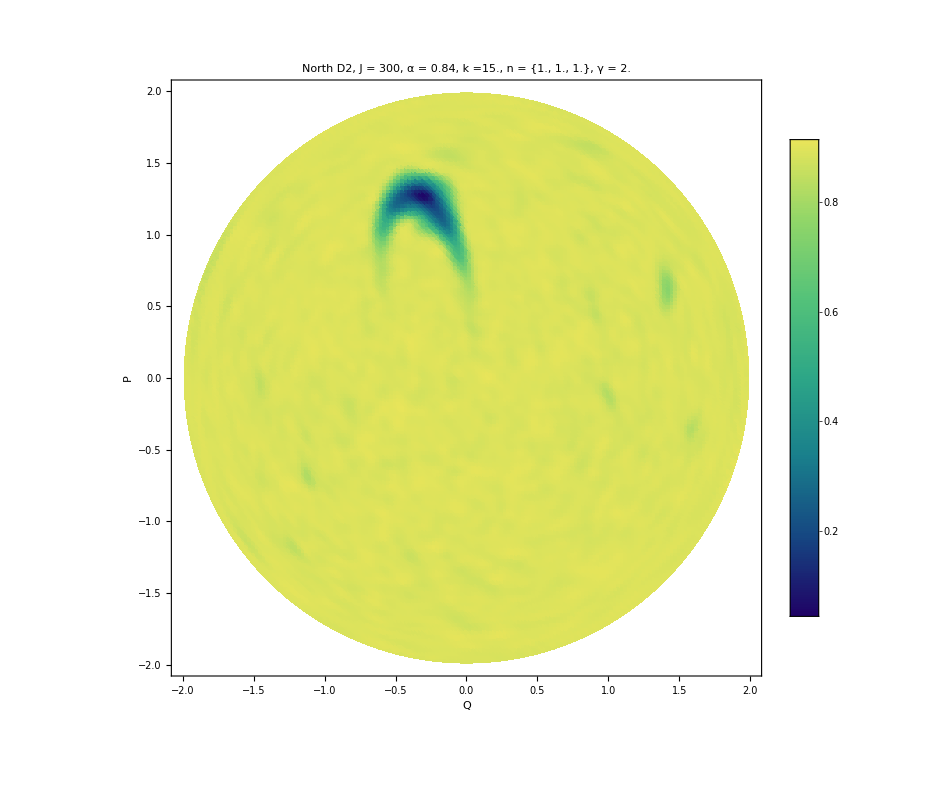

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k]<>", n = "<>ToString[N[n]]<>", γ = "<>ToString[γ],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,PlotRange->{{-2,2},{-2,2},{0,1}},RegionFunction->Function[{q,p,val},q^2+p^2<=4]]
```

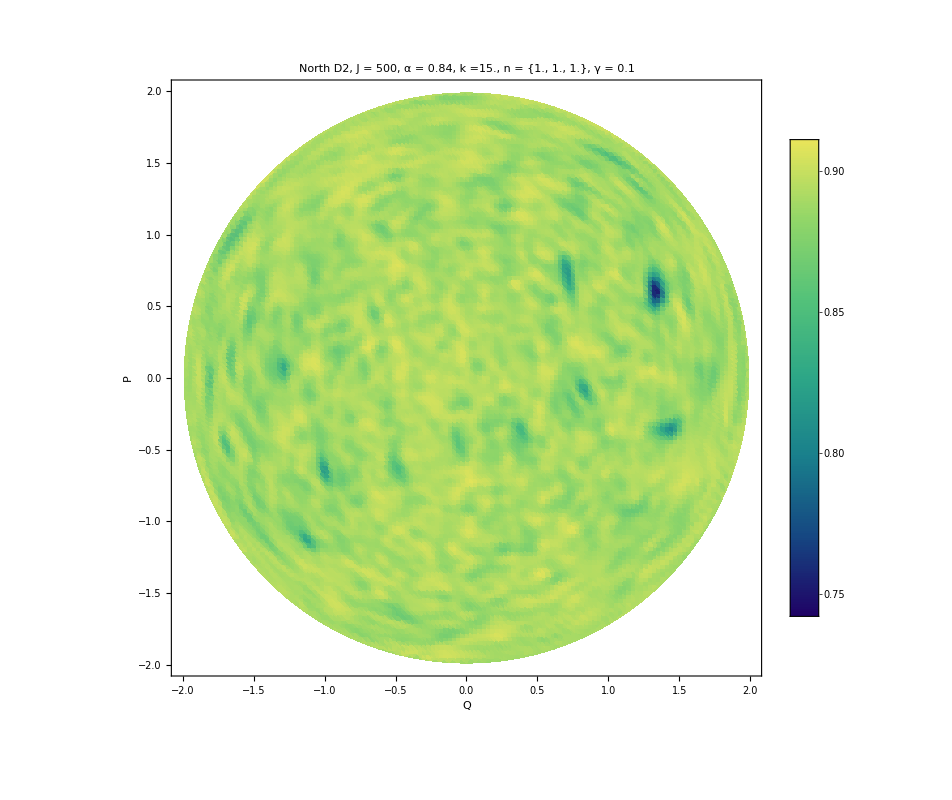

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k]<>", n = "<>ToString[N[n]]<>", γ = "<>ToString[γ],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,PlotRange->{{-2,2},{-2,2},{0,1}},RegionFunction->Function[{q,p,val},q^2+p^2<=4]]
```

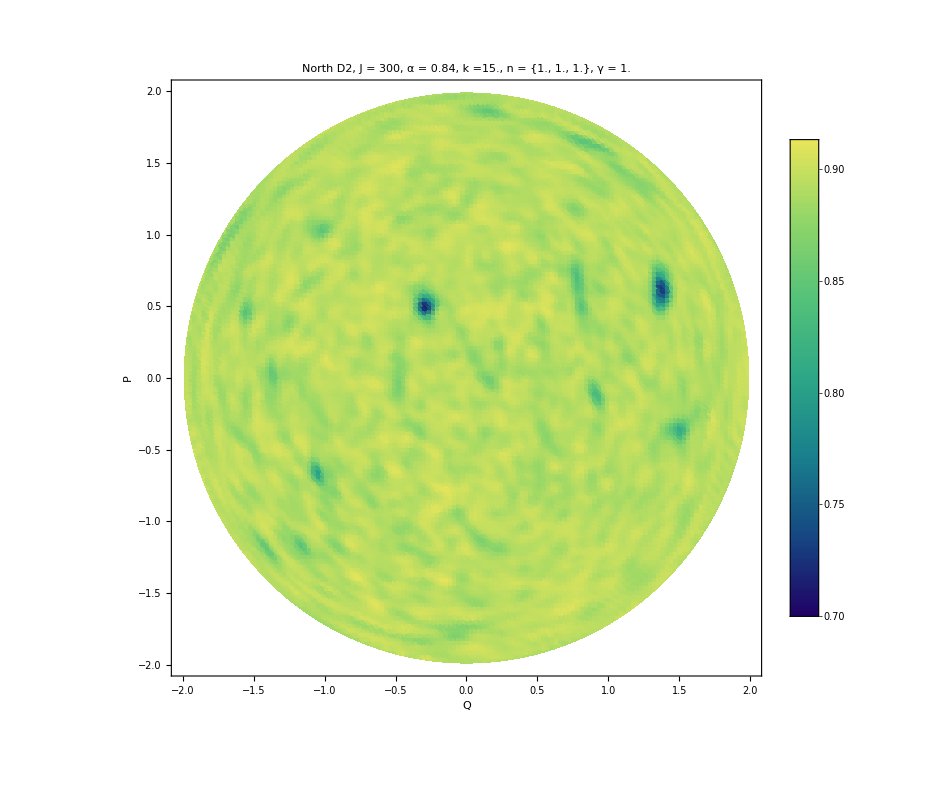

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k]<>", n = "<>ToString[N[n]]<>", γ = "<>ToString[γ],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,PlotRange->{{-2,2},{-2,2},{0,1}},RegionFunction->Function[{q,p,val},q^2+p^2<=4]]
```

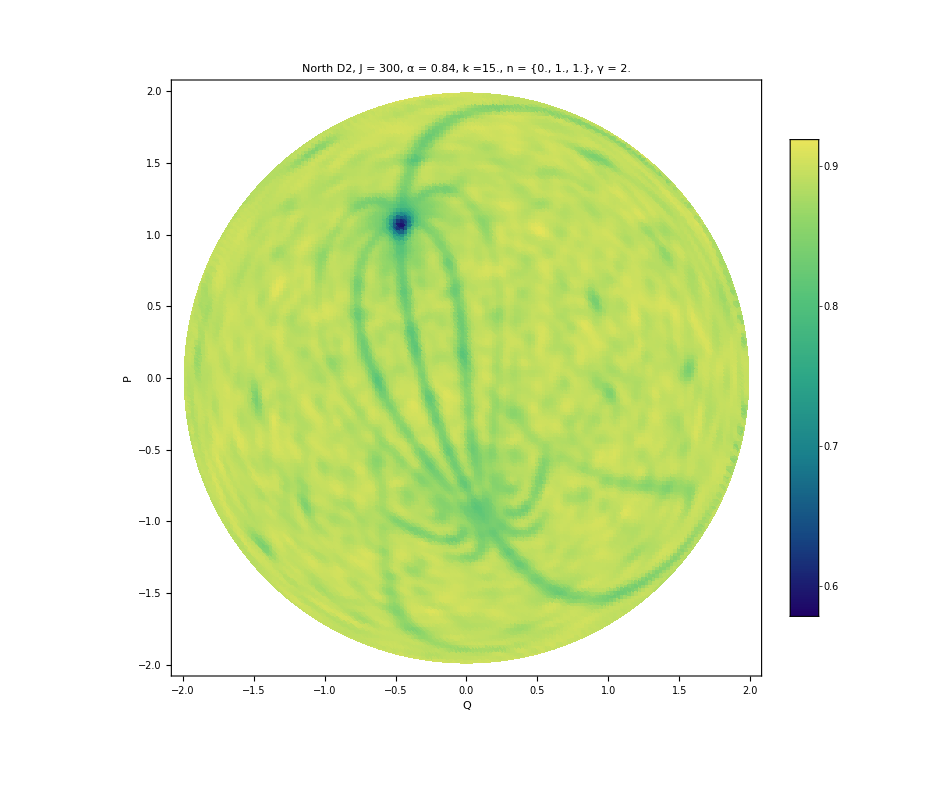

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k]<>", n = "<>ToString[N[n]]<>", γ = "<>ToString[γ],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,PlotRange->{{-2,2},{-2,2},{0,1}},RegionFunction->Function[{q,p,val},q^2+p^2<=4]]
```

## r ratios

```mathematica
J=500;
x=Sx[J];
y=Sy[J];
z=Sz[J];
```

```mathematica
x2=x.x;
```

```mathematica
Clear[Floqb];
Floqb[n_,α_,k_,γ_]:=Module[{u=Normalize[n]},
N[MatrixExp[(-I*k/(2J))(x2)-I*γ*z]].N[MatrixExp[(-I*α)(u.{x,y,z})]]
];
```

```mathematica
glist=Table[i,{i,0,2,0.05}];
glist//Length
```

41

```mathematica
α=0.84;
k=15.;
n={0,1,1};
```

```mathematica
data={};
Do[
mat=Floqb[n,α,k,g];
{eigenval,eigenvec}=Eigensystem[mat];
eigenvec=Orthogonalize[eigenvec];
AppendTo[data,{g,MeanLevelSpacingRatio[Sort[Arg[eigenval]]]}];
,{g,glist}];
```

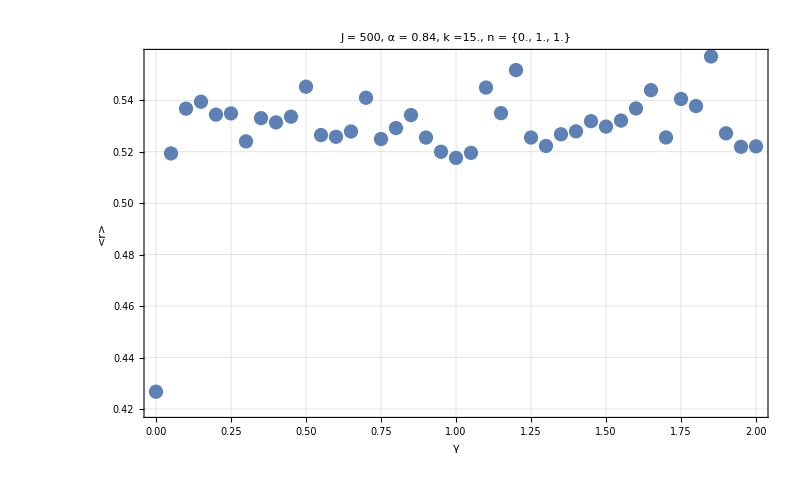

```mathematica
ListPlot[data,PlotRange->All,PlotTheme->"Detailed",ImageSize->800,PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k]<>", n = "<>ToString[N[n]],25,Black],FrameLabel->{Style["γ",40,Black],Rotate[Style["<r>",40,Black],-90Degree]}]
```

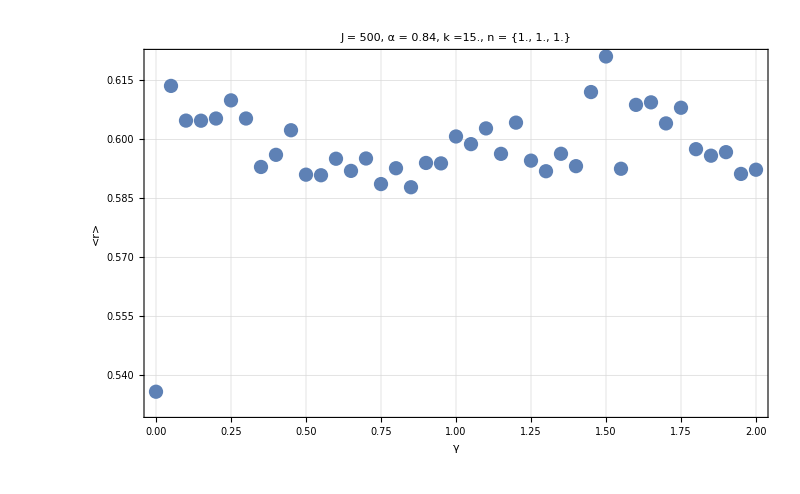

```mathematica
ListPlot[data,PlotRange->All,PlotTheme->"Detailed",ImageSize->800,PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k]<>", n = "<>ToString[N[n]],25,Black],FrameLabel->{Style["γ",40,Black],Rotate[Style["<r>",40,Black],-90Degree]}]
```

# Breaking time reversal symmetry 2

## Phase space

```mathematica
Clear[Rz,Rx,Ry,MeanLevelSpacingRatio];
Rx[J_,θ_]:=MatrixExp[-I(N[θ])Sx[J]];
Ry[J_,θ_]:=MatrixExp[-I(N[θ])Sy[J]];
Rz[J_,θ_]:=MatrixExp[-I(N[θ])Sz[J]];
MeanLevelSpacingRatio[eigenvalues_]:=Mean[Min/@Transpose[{#,1/#}]&[Ratios[Differences[Sort[eigenvalues]]]]]
```

```mathematica
Clear[J];
J=300;
```

```mathematica
cohes=ParallelTable[Quiet[a2[J,i[[1 ]],i[[2]]]],{i,region},DistributedContexts->Full,Method->"CoarsestGrained"];
```

```mathematica
Clear[Floqb];
Floqb[J_,n_,α_,k_,γ_]:=Module[{u=Normalize[n],x=Sx[J],y=Sy[J],z=Sz[J]},
N[MatrixExp[(-I*k/(2J))(x.x)]].N[MatrixExp[(-I*α)(u.{x,y,z})]].N[MatrixExp[(-I*γ)(y)]]
];
```

```mathematica
α=0.84;
k=4.;
n={1,1,1};
γ=1.;
```

```mathematica
mat=Floqb[J,n,α,k,γ];
{eigenval,eigenvec}=Eigensystem[mat];
eigenvec=Orthogonalize[eigenvec];
(*South pole*)
(*mat=ConjugateTranspose[rotation3].ConjugateTranspose[rotation].Floq[J,α,k,τ].rotation.rotation3;*)
(*matM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
matm=Table[mat[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
{eigenvalM,eigenvecM}=Eigensystem[matM];
{eigenvalm,eigenvecm}=Eigensystem[matm];*)
(*zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
eigenval=Riffle[eigenvalM,eigenvalm];
eigenvec=Riffle[neweigenvecM,neweigenvecm];*)
```

```mathematica
MeanLevelSpacingRatio[Sort[Arg[eigenval]]]
```

0.500134

```mathematica
q=2;
d2M=ParallelTable[Total[Abs[Conjugate[eigenvec].i]^(2q)],{i,cohes},DistributedContexts->Full];
```

```mathematica
newd2M=Transpose[{region[[All,1]],region[[All,2]],(1-q)Log[d2M]/Log[2J+1]}];
```

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", n = "<>ToString[N[n]]<>", γ = "<>ToString[γ],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,PlotRange->{{-2,2},{-2,2},{0,1}},RegionFunction->Function[{q,p,val},q^2+p^2<=4]]
```

-Graphics-

```mathematica
Show[{d2plotM,classic}]
```

-Graphics-

## examples

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k]<>", n = "<>ToString[N[n]]<>", γ = "<>ToString[γ],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,PlotRange->{{-2,2},{-2,2},{0,1}},RegionFunction->Function[{q,p,val},q^2+p^2<=4]]
```

-Graphics-

```mathematica
Show[{d2plotM,classic}]
```

-Graphics-

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k]<>", n = "<>ToString[N[n]]<>", γ = "<>ToString[γ],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,PlotRange->{{-2,2},{-2,2},{0,1}},RegionFunction->Function[{q,p,val},q^2+p^2<=4]]
```

-Graphics-

```mathematica
Show[{d2plotM,classic}]
```

-Graphics-

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k]<>", n = "<>ToString[N[n]]<>", γ = "<>ToString[γ],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,PlotRange->{{-2,2},{-2,2},{0,1}},RegionFunction->Function[{q,p,val},q^2+p^2<=4]]
```

-Graphics-

```mathematica
Show[{d2plotM,classic}]
```

-Graphics-

```mathematica
Show[{d2plotM,classic}]
```

-Graphics-

## r ratios

```mathematica
J=1000;
x=Sx[J];
y=Sy[J];
z=Sz[J];
```

```mathematica
x2=x.x;
```

```mathematica
Clear[Floqb];
Floqb[n_,α_,k_,γ_]:=Module[{u=Normalize[n]},
N[MatrixExp[(-I*γ)(y)]].N[MatrixExp[(-I*k/(2J))(x2)-I*γ*z]].N[MatrixExp[(-I*α)(u.{x,y,z})]]
];
```

```mathematica
glist=Table[i,{i,0,2,0.01}];
glist//Length
```

201

```mathematica
α=0.84;
k=4.;
n={1,1,1};
```

```mathematica
Clear[eval,ratios];
eval[g_]:=Module[{mat=Floqb[n,α,k,g]},Sort[Arg[Eigenvalues[mat]]]];
ratios[g_]:=MeanLevelSpacingRatio[eval[g]];
```

```mathematica
DistributeDefinitions[eval,ratios,Floqb,n,α,k,MeanLevelSpacingRatio];
data=ParallelTable[ratios[g],{g,glist},DistributedContexts->Full];
```

```mathematica
ListPlot[Transpose[{glist,data}],PlotRange->All,PlotTheme->"Detailed",ImageSize->800,PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", n = "<>ToString[N[n]],25,Black],FrameLabel->{Style["γ",40,Black],Rotate[Style["<r>",40,Black],-90Degree]}]
```

-Graphics-

```mathematica
ListPlot[Transpose[{glist,data}],PlotRange->All,PlotTheme->"Detailed",ImageSize->800,PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", n = "<>ToString[N[n]],25,Black],FrameLabel->{Style["γ",40,Black],Rotate[Style["<r>",40,Black],-90Degree]}]
```

-Graphics-